```mathematica
ode=y''[x]-y'[x]+2x-1==0
```

-1+2 x-y'[x]+y''[x]==0

```mathematica
generalSolution=FullSimplify[DSolve[ode,y[x],x]]
```

{{y[x]→x+x^2+ⅇ^x C[1]+C[2]}}

```mathematica
particularSolution=FullSimplify[DSolve[{ode,y[0]==1,y[1]==3},y[x],x]]
```

{{y[x]→1+x+x^2}}

```mathematica
ya[x_]:=y[x]/.particularSolution[[1]]
```

```mathematica
FullSimplify[D[ya[x],x]]
```

1+2 x

```mathematica
FullSimplify[D[ya[x],x,x]]
```

2

```mathematica
dyadx[x_]:=1+2x
```

```mathematica
d2yadx2[x_]:=2
```

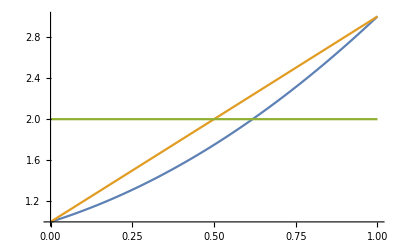

```mathematica
Plot[{ya[x],dyadx[x],d2yadx2[x]},{x,0,1}]
```

```mathematica
Limit[y/(√(1-y^2)),y->1]
```

(-ⅈ) ∞